```mathematica
Expand[4+5x+8x^2+x^3-(4/11)(11-6x+4x^2)]
```

(79 x)/11+(72 x^2)/11+x^3

```mathematica
CoefficientList[(4+5x+8x^2+x^3)(4/11)-((16/79+C1*x)/x)((79 x)/11+(72 x^2)/11+x^3),x]
```

{0,428/869-(79 C1)/11,2352/869-(72 C1)/11,4/11-C1}

```mathematica
Solve[428/869-(79 C1)/11==0]
```

{{C1→428/6241}}

```mathematica
Expand[(4+5x+8x^2+x^3)(4/11)-((16/79+C1*x)/x)((79 x)/11+(72 x^2)/11+x^3)/.{C1->428/6241}]
```

(154992 x^2)/68651+(20256 x^3)/68651

```mathematica
CoefficientList[x((4+5x+8x^2+x^3)(4/11)((16/79+428/6241*x)/x)-((C3+C2 x+ C1 x^2 + C0 x^3)/x^3)*((154992 x^2)/68651+(20256 x^3)/68651)),x]
```

{256/869-(154992 C3)/68651,32128/68651-(154992 C2)/68651-(20256 C3)/68651,49008/68651-(154992 C1)/68651-(20256 C2)/68651,18752/68651-(154992 C0)/68651-(20256 C1)/68651,1712/68651-(20256 C0)/68651}

```mathematica
ToRules[Reduce[{256/869-(154992 C3)/68651,32128/68651-(154992 C2)/68651-(20256 C3)/68651,49008/68651-(154992 C1)/68651-(20256 C2)/68651,18752/68651-(154992 C0)/68651-(20256 C1)/68651}=={0,0,0,0},{C3,C2,C1,C0}]]
```

{C3→1264/9687,C2→5950424/31279323,C1→29425109855/101000933967,C0→27040301844298/326132015779443}

```mathematica
Expand[((4+5x+8x^2+x^3)(4/11)((16/79+428/6241*x)/x)-((C3+C2 x+ C1 x^2 + C0 x^3)/x^3)*((154992 x^2)/68651+(20256 x^3)/68651))/.{C3->1264/9687,C2->5950424/31279323,C1->29425109855/101000933967,C0->27040301844298/326132015779443}]
```

(3536552285435376 x^3)/7463096338424847131

```mathematica
q1=4/11
q2=((16/79+C1*x)/x)/.{C1->428/6241}
q3=((C3+C2 x+ C1 x^2 + C0 x^3)/x^3)/.{C3->1264/9687,C2->5950424/31279323,C1->29425109855/101000933967,C0->27040301844298/326132015779443}
```

4/11

(16/79+(428 x)/6241)/x

(1264/9687+(5950424 x)/31279323+(29425109855 x^2)/101000933967+(27040301844298 x^3)/326132015779443)/x^3

```mathematica
CoefficientList[x^4*((4+5x+8x^2+x^3)*q1*q2*q3-((c7+c6 x+ c5 x^2+ c4 x^3+c3 x^4+c2 x^5+c1 x^6+c0 x^7)/x^7)*(3536552285435376 x^3)/7463096338424847131),x]
```

{4096/106557-(3536552285435376 c7)/7463096338424847131,1061056512/9060577229-(3536552285435376 c6)/7463096338424847131,1858275696371200/6933815117768517-(3536552285435376 c5)/7463096338424847131,7437996882306872576/22389289015274541393-(3536552285435376 c4)/7463096338424847131,6761442294242207824/22389289015274541393-(3536552285435376 c3)/7463096338424847131,3213103101959260832/22389289015274541393-(3536552285435376 c2)/7463096338424847131,223241053289329712/7463096338424847131-(3536552285435376 c1)/7463096338424847131,46292996757438176/22389289015274541393-(3536552285435376 c0)/7463096338424847131}

```mathematica
ToRules[Reduce[{4096/106557-(3536552285435376 c7)/7463096338424847131,1061056512/9060577229-(3536552285435376 c6)/7463096338424847131,1858275696371200/6933815117768517-(3536552285435376 c5)/7463096338424847131,7437996882306872576/22389289015274541393-(3536552285435376 c4)/7463096338424847131,6761442294242207824/22389289015274541393-(3536552285435376 c3)/7463096338424847131,3213103101959260832/22389289015274541393-(3536552285435376 c2)/7463096338424847131,223241053289329712/7463096338424847131-(3536552285435376 c1)/7463096338424847131,46292996757438176/22389289015274541393-(3536552285435376 c0)/7463096338424847131}=={0,0,0,0,0,0,0,0},{c0,c1,c2,c3,c4,c5,c6,c7}]]
```

{c0→2893312297339886/663103553519133,c1→13952565830583107/221034517839711,c2→200818943872453802/663103553519133,c3→422590143390137989/663103553519133,c4→464874805144179536/663103553519133,c5→375023263973912800/663103553519133,c6→6069308378351872/24559390871079,c7→53789596065113344/663103553519133}

```mathematica
q4=((c7+c6 x+ c5 x^2+ c4 x^3+c3 x^4+c2 x^5+c1 x^6+c0 x^7)/x^7)/.{c0->2893312297339886/663103553519133,c1->13952565830583107/221034517839711,c2->200818943872453802/663103553519133,c3->422590143390137989/663103553519133,c4->464874805144179536/663103553519133,c5->375023263973912800/663103553519133,c6->6069308378351872/24559390871079,c7->53789596065113344/663103553519133}
```

1/x^7(53789596065113344/663103553519133+(6069308378351872 x)/24559390871079+(375023263973912800 x^2)/663103553519133+(464874805144179536 x^3)/663103553519133+(422590143390137989 x^4)/663103553519133+(200818943872453802 x^5)/663103553519133+(13952565830583107 x^6)/221034517839711+(2893312297339886 x^7)/663103553519133)

```mathematica
q1
ExpandNumerator[Together[Expand[q2]]]
ExpandNumerator[Together[Expand[q3]]]
ExpandNumerator[Together[Expand[q4]]]
```

4/11

(1264+428 x)/(6241 x)

(42555060178096+62041744760984 x+95013679721795 x^2+27040301844298 x^3)/(326132015779443 x^3)

1/(663103553519133 x^7)(53789596065113344+163871326215500544 x+375023263973912800 x^2+464874805144179536 x^3+422590143390137989 x^4+200818943872453802 x^5+41857697491749321 x^6+2893312297339886 x^7)

```mathematica
ExpandNumerator[Together[Expand[1/q1-1/q2+1/q3-1/q4]]]
```

(11-6 x+4 x^2)/(4+5 x+8 x^2+x^3)

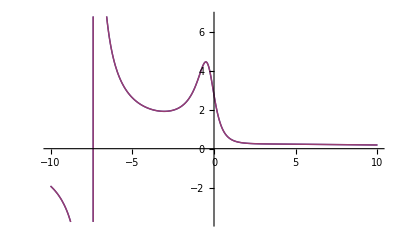

```mathematica
Plot[{(11-6 x+4 x^2)/(4+5 x+8 x^2+x^3), 1/q1-1/q2+1/q3-1/q4},{x,-10,10}]
```

```mathematica
Together[Expand[1/q1-1/q2+1/q3-1/q4]]
```

(11-6 x+4 x^2)/(4+5 x+8 x^2+x^3)